```mathematica
P0={P0x,P0y}
P1={P1x,P1y}
P2={P2x,P2y}
```

{P0x,P0y}

{P1x,P1y}

{P2x,P2y}

```mathematica
pt = {P0, P1,P2}
```

{{P0x,P0y},{P1x,P1y},{P2x,P2y}}

```mathematica
C1rule={P0x->0,P1x->P11x,P2x->1,P0y->0,P1y->P11y,P2y->0}
C2rule={P0x->0,P1x->P12x,P2x->1,P0y->-0.25,P1y->P12y,P2y->0.5}
```

{P0x→0,P1x→P11x,P2x→1,P0y→0,P1y→P11y,P2y→0}

{P0x→0,P1x→P12x,P2x→1,P0y→-0.25,P1y→P12y,P2y→0.5}

```mathematica
C1=pts/.C1rule
C2=pts/.C2rule
```

{{0,0},{P11x,P11y},{1,0}}

{{0,-0.25},{P12x,P12y},{1,0.5}}

```mathematica
maxd=(C1[[2]]-C2[[2]]).(C1[[2]]-C2[[2]])
```

(P11x-P12x)^2+(P11y-P12y)^2

```mathematica
(C1[[2]]-C1[[1]]).(C1[[2]]-C1[[1]])
```

P11x^2+P11y^2

```mathematica
mind = (C1[[2]]-C1[[1]]).(C1[[2]]-C1[[1]]) + (C1[[2]]-C1[[3]]).(C1[[2]]-C1[[3]]) + (C2[[2]]-C2[[1]]).(C2[[2]]-C2[[1]])+ (C2[[2]]-C2[[3]]).(C2[[2]]-C2[[3]])
```

(-1+P11x)^2+P11x^2+2 P11y^2+(-1+P12x)^2+P12x^2+(-0.5+P12y)^2+(0.25+P12y)^2

```mathematica
f=mind + 1/maxd
```

(-1+P11x)^2+P11x^2+2 P11y^2+(-1+P12x)^2+P12x^2+1/((P11x-P12x)^2+(P11y-P12y)^2)+(-0.5+P12y)^2+(0.25+P12y)^2

```mathematica
vars={{P11x,(P0x+P2x)/2}/.C1rule,{P12x,(P0x+P2x)/2}/.C2rule,{P11y,(P0y+P2y)/2}/.C1rule,{P12y,(P0y+P2y)/2}/.C2rule}
minSol=FindMinimum[f,vars]
```

{{P11x,1/2},{P12x,1/2},{P11y,0},{P12y,0.125}}

{3.04284,{P11x→0.5,P12x→0.5,P11y→-0.453889,P12y→0.578889}}

```mathematica
(*minSol=FindMinimum[{f,{P11x,P11y}∈Disk[]&&{P12x,P12y}∈Disk[]},{P11x,P12x,P11y,P12y}]*)
```

{2.17862,{P11x→0.5,P12x→0.5,P11y→0.326388,P12y→-0.826388}}

```mathematica
(D[f,{P12x,2}]//Simplify)/.minSol[[2]]
```

2.24207

```mathematica
minSol[[2]]
```

{P11x→0.5,P12x→0.5,P11y→-0.453889,P12y→0.578889}

```mathematica
{(minSol[[2]][[1]]),(minSol[[2]][[3]])}
```

{P11x→0.5,P11y→-0.453889}

```mathematica
f/.{(minSol[[2]][[1]]),(minSol[[2]][[3]])}
```

0.91203+Abs[-1+P12x]^2+Abs[P12x]^2+1/(Abs[0.5-P12x]^2+Abs[-0.453889-P12y]^2)+Abs[-0.5+P12y]^2+Abs[0.25+P12y]^2

```mathematica
Plot3D[f/.{(minSol[[2]][[1]]),(minSol[[2]][[3]])},{P12x,-1,1},{P12y,-1,1}]
```

-Graphics3D-

```mathematica
f1=BezierFunction[C1]/.minSol[[2]]
f2=BezierFunction[C2]/.minSol[[2]]
```

BezierFunction[{{0., 1.}}, <>]

BezierFunction[{{0., 1.}}, <>]

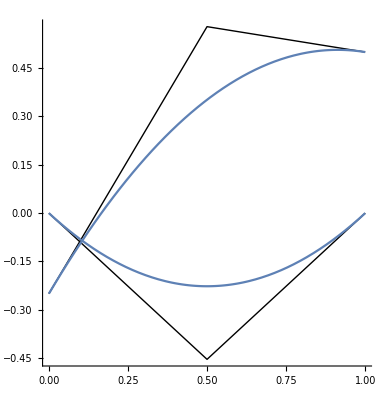

```mathematica
Show[Graphics[{Line[C1],Line[C2]}]/.minSol[[2]], ParametricPlot[{f1[t],f2[t]}/.minSol[[2]],{t,0,1},PlotRange->Full],Axes-> True]
```

```mathematica
f3=BezierFunction[C1-C2]/.minSol[[2]]
```

BezierFunction[{{0., 1.}}, <>]

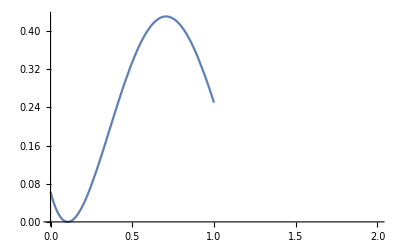

```mathematica
Plot[Norm[f3[t]]^2,{t,0,2}]
```

```mathematica
FindRoot[Norm[f3[t]]^2==0,{t,0.5}]
```

{t→0.10529}

```mathematica
f3[0.1052899672878802]
```

{0.,-3.14115×10^-8}

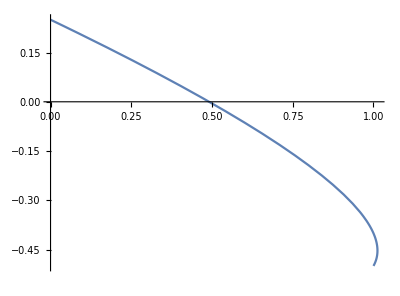

```mathematica
ParametricPlot[{f3[t]}/.minSol[[2]],{t,0,2},PlotRange->Full]
```

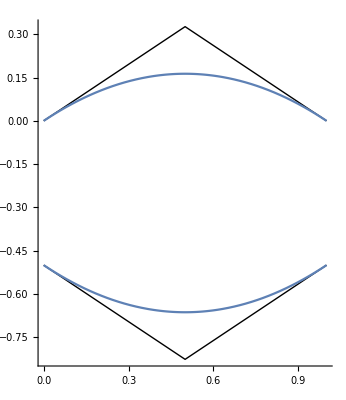

```mathematica
Show[Graphics[{Line[C1],Line[C2]}]/.minSol[[2]], ParametricPlot[{f1[t],f2[t]}/.minSol[[2]],{t,0,1},PlotRange->Full],Axes-> True]
```

{P11x→0,P11y→0.5,P12x→0.5,P12y→-0.5}

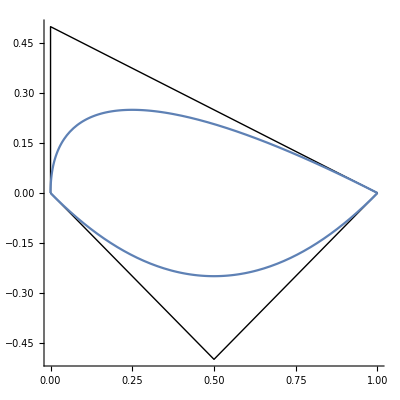

{P0x→0,P1x→1.5,P2x→1,P0y→0,P1y→0.5,P2y→0}

```mathematica
example={P11x-> 0, P11y-> 0.5, P12x-> 0.5, P12y-> -0.5}
Show[Graphics[{Line[C1],Line[C2]}]/.example,ParametricPlot[{f1[t],f2[t]}/.example,{t,0,1},PlotRange->Full],Axes-> True]
```

```mathematica
P0/.C1rule
```

{0,0}

```mathematica
P1
```

{P1x,P1y}

```mathematica
c=P0(1-t)^2+t^2P2
```

{P0x (1-t)^2+P2x t^2,P0y (1-t)^2+P2y t^2}

```mathematica
α=2 t (1-t)
```

2 (1-t) t

```mathematica
c+α P1//MatrixForm
```

(P0x (1-t)^2+2 P1x (1-t) t+P2x t^2
P0y (1-t)^2+2 P1y (1-t) t+P2y t^2)

```mathematica
normB=(c-α P1).(c-α P1)
```

(P0x (1-t)^2-2 P1x (1-t) t+P2x t^2)^2+(P0y (1-t)^2-2 P1y (1-t) t+P2y t^2)^2

```mathematica
Collect[D[normB,t],t]//Simplify
```

4 (-P0x^2-P0y^2-P0x P1x-P0y P1y+(3 P0x^2+3 P0y^2+2 (P1x^2+P1y^2)+P0x (6 P1x+P2x)+P0y (6 P1y+P2y)) t-3 (P0x^2+P0y^2+2 P1x^2+2 P1y^2+P1x P2x+P0x (3 P1x+P2x)+P1y P2y+P0y (3 P1y+P2y)) t^2+(P0x^2+P0y^2+4 P1x^2+4 P1y^2+4 P1x P2x+P2x^2+2 P0x (2 P1x+P2x)+4 P1y P2y+P2y^2+2 P0y (2 P1y+P2y)) t^3)

```mathematica
Solve[D[normB,t]==0,t,Reals]
```

$Aborted

```mathematica
Solve[{D[(normB/.%592)[[1]],P1x]==0,D[(normB/.%592)[[1]],P1y]==0},{P1x,P1y}]
```

$Aborted

```mathematica
Integrate[normB,t]//FullSimplify
```

P0x^2 t+P0y^2 t-2 P0x (P0x+P1x) t^2-2 P0y (P0y+P1y) t^2+2/3 (3 P0x^2+2 P1x^2+P0x (6 P1x+P2x)) t^3+2/3 (3 P0y^2+2 P1y^2+P0y (6 P1y+P2y)) t^3-(P0x+P1x) (P0x+2 P1x+P2x) t^4-(P0y+P1y) (P0y+2 P1y+P2y) t^4+1/5 (P0x+2 P1x+P2x)^2 t^5+1/5 (P0y+2 P1y+P2y)^2 t^5

```mathematica
intnormB=Integrate[normB,{t,0,1}]
```

P0x^2/5+P0y^2/5-(P0x P1x)/5+(2 P1x^2)/15-(P0y P1y)/5+(2 P1y^2)/15+(P0x P2x)/15-(P1x P2x)/5+P2x^2/5+(P0y P2y)/15-(P1y P2y)/5+P2y^2/5

```mathematica
intnormB//Simplify
```

1/15 (3 P0x^2+3 P0y^2+2 P1x^2+2 P1y^2-3 P1x P2x+3 P2x^2+P0x (-3 P1x+P2x)-3 P1y P2y+3 P2y^2+P0y (-3 P1y+P2y))

```mathematica
Solve[{D[intnormB,P1x]==0,
D[intnormB,P1y]==0},{P1x,P1y}]
```

{{P1x→(3 (P0x+P2x))/4,P1y→(3 (P0y+P2y))/4}}

```mathematica
C1
```

{{0,0},{3/4,0},{1,0}}

```mathematica
{(1-t)^2,2t(1-t),t^2}.C1
```

{3/2 (1-t) t+t^2,0}

```mathematica
bez[points_]:={(1-t)^2,2t(1-t),t^2}.points
```

```mathematica
minRule={P1mx->(3 (P0x+P2x))/4,P1my->(3 (P0y+P2y))/4}
```

{P1mx→(3 (P0x+P2x))/4,P1my→(3 (P0y+P2y))/4}

```mathematica
(*NO THIS RULE APPLIES TO THE DIFFERENCE OF THE TWO CURVES!*)
```

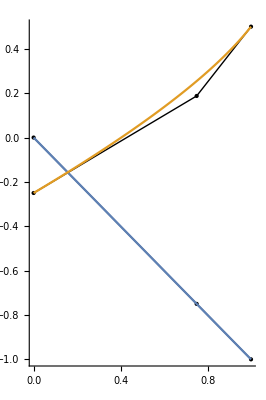

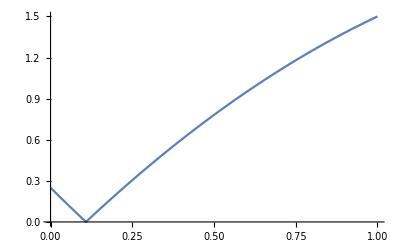

```mathematica
C1rule={P0x->0,P1x->P1mx,P2x->1,P0y->0,P1y->P1my,P2y->-1};
C2rule={P0x->0,P1x->P1mx,P2x->1,P0y->-1/4,P1y->P1my,P2y->1/2};
C1rule=C1rule/.(minRule/.C1rule);
C2rule=C2rule/.(minRule/.C2rule);
C1=pts/.C1rule;
C2=pts/.C2rule;
Show[Graphics[{Line[C1],Line[C2]}], Graphics[{Point[C1],Point[C2]}],ParametricPlot[{bez[C1],bez[C2]},{t,0,1},PlotRange->Full],Axes-> True]
Plot[Norm[bez[C1-C2]],{t,0,1},PlotRange->{0,All}]
```

√(Abs[-3 (1-t)^2-9/2 (1-t) t]^2+Abs[1/4 (1-t)^2-15/8 (1-t) t-(3 t^2)/2]^2)

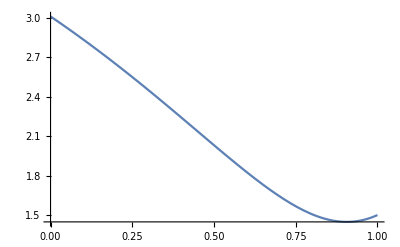

```mathematica
Norm[bez[C1-C2]]
```

```mathematica
Graphics[Point[C1]]
```

-Graphics-

```mathematica
c.c
```

(P0x (1-t)^2+P2x t^2)^2+(P0y (1-t)^2+P2y t^2)^2

```mathematica
Collect[D[c.c ,t]//Simplify,t]
```

-2 P0x^2-2 P0y^2+(2 P0x^2+2 P0y^2+4 P0x P2x+4 P0y P2y) t+(-6 P0x P2x-6 P0y P2y) t^2+(4 P2x^2+4 P2y^2) t^3

{P0x (1-t)+P2x t^2,P0y (1-t)+P2y t^2}

{Cx,Cy}

```mathematica
Assuming[0≤ t≤ 1,Solve[D[normB,t]==0,t]]
```

{{t→(2 P0x P1x+4 P1x^2+2 P0y P1y+4 P1y^2+P0x P2x+2 P1x P2x+P0y P2y+2 P1y P2y)/(2 (4 P1x^2+4 P1y^2+4 P1x P2x+P2x^2+4 P1y P2y+P2y^2))-(-36 (1)^2+24 1 (1))/(6 2^1 (1) (1)^(1/3))+(1)^(1/3)/(12 2^(1/3) (4 P1x^2+4 P1y^2+4 P1x P2x+P2x^2+4 P1y P2y+P2y^2))},{t→1},{t→1}}
 |  |  |  |

```mathematica
D[normB,t]==0//Simplify
```

```mathematica
Solve[2 (P0x+P1x (2-4 t)-2 P2x t) (P0x (-1+t)-t (2 P1x (-1+t)+P2x t))+2 (P0y+P1y (2-4 t)-2 P2y t) (P0y (-1+t)-t (2 P1y (-1+t)+P2y t))==0,t]
```

{{t→(2 P0x P1x+4 P1x^2+2 P0y P1y+4 P1y^2+P0x P2x+2 P1x P2x+P0y P2y+2 P1y P2y)/(2 (4 P1x^2+4 P1y^2+4 P1x P2x+P2x^2+4 P1y P2y+P2y^2))-(-36 (1)^2+24 1 (1))/(6 2^1 (1) (1)^(1/3))+(1)^(1/3)/(12 2^(1/3) (4 P1x^2+4 P1y^2+4 P1x P2x+P2x^2+4 P1y P2y+P2y^2))},{t→1},{t→1}}
 |  |  |  |

```mathematica
normB/.%384[[1]]
normB/.%384[[2]]
normB/.%384[[3]]
```

(P0x (1-1/(2 1)+1/1-(1)^(1/3)/(12 2^111 (4 P1x^2+4+P2y^2)))-1+P2x 1)^2+(1)^2
 |  |  |  |

(P2x (1/(2 1)+1-1/1)^2+1-2 2 (1-1-1+((1) 1)/1))^2+(P2y (1)^2+P0y 1-2 P1y (1) (1))^2
 |  |  |  |

(P2x (1/(2 1)+1-1/1)^2+1-2 2 (1-1-1+((1) 1)/1))^2+(P2y (1)^2+P0y 1-2 P1y (1) (1))^2
 |  |  |  |

```mathematica
Length[%384]
```

3

```mathematica
D[intnormB,{P1x,2}]
D[intnormB,{P1y,2}]
```

4/15